```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
l=Flatten @Import["test1.dat"];
nn=Length[l];
```

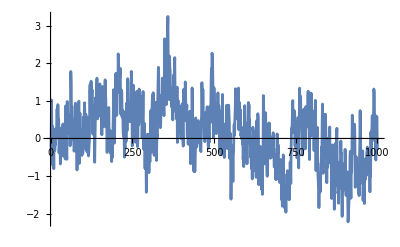

```mathematica
ListLinePlot[Take[l,UpTo[1000]]]
```

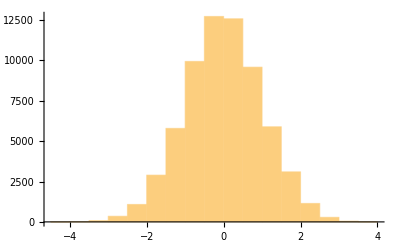

-5.78533×10^-9

1.00001

```mathematica
Histogram[l]
avg=Mean[l]
std=StandardDeviation[l]
```

{{0,1.},{1,0.864914},{2,0.801409},{3,0.770604},{4,0.745165},{5,0.726801},{6,0.711344},{7,0.7006},{8,0.688834},{9,0.679682},{10,0.670485},{11,0.662204},{12,0.655088},{13,0.649238},{14,0.642767},{15,0.637429},{16,0.631847},{17,0.626633},{18,0.621519},{19,0.616168},{20,0.612046},{21,0.607119},{22,0.602141},{23,0.596149},{24,0.592541},{25,0.590212},{26,0.586143},{27,0.583383},{28,0.581772},{29,0.579301},{30,0.577653},{31,0.575385},{32,0.572704},{33,0.570101},{34,0.56835},{35,0.566042},{36,0.563854},{37,0.562514},{38,0.561563},{39,0.559789},{40,0.558961},{41,0.55636},{42,0.554985},{43,0.553888},{44,0.552675},{45,0.549898},{46,0.547242},{47,0.546175},{48,0.54367},{49,0.54085},{50,0.539786},{51,0.538817},{52,0.536717},{53,0.534793},{54,0.533583},{55,0.53098},{56,0.529558},{57,0.528869},{58,0.527777},{59,0.526547},{60,0.524993},{61,0.523863},{62,0.522545},{63,0.52176},{64,0.520276},{65,0.519728},{66,0.518824},{67,0.517978},{68,0.517001},{69,0.5157},{70,0.51538},{71,0.513731},{72,0.511299},{73,0.510507},{74,0.508744},{75,0.506873},{76,0.505806},{77,0.502763},{78,0.502654},{79,0.50284},{80,0.502071},{81,0.50162},{82,0.500485},{83,0.498937},{84,0.498803},{85,0.497983},{86,0.496591},{87,0.494736},{88,0.493749},{89,0.493263},{90,0.492677},{91,0.492067},{92,0.489931},{93,0.487497},{94,0.486437},{95,0.485135},{96,0.483576},{97,0.483623},{98,0.482407},{99,0.481726},{100,0.482111}}

{a→0.85721,b→0.0812907}

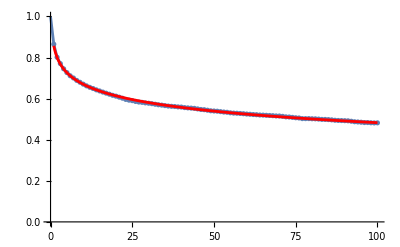

```mathematica
cf=Table[{i,CorrelationFunction[l-avg,i]},{i,0,100}]
p1=ListPlot[cf,PlotRange->{0,1},Joined->True,Mesh->All];
fnc=a-b Log[t];
sol=FindFit[Drop[cf,1],fnc,{a,b},t]
fnc=fnc/.sol;
p2=Plot[fnc,{t,1,100},PlotStyle->Red];
Show[p1,p2]
(* Logarithmic autocorrelation, see Kechner 1982 *)
```

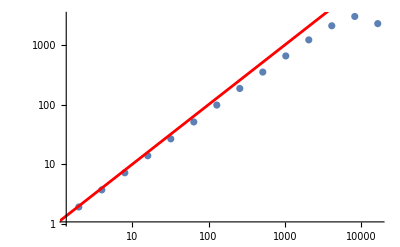

```mathematica
tab=Table[{2^i,StandardDeviation[Map[Total,Partition[l,2^i]]]},{i,14}];
p1=ListLogLogPlot[tab];
p2=LogLogPlot[{1x^(1)},{x,1,Length[l]},PlotStyle->{Red}];
Show[p1,p2]
```

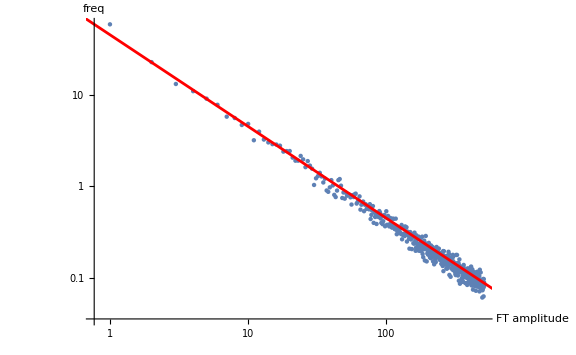

```mathematica
sz=1024;
pl=Partition[l,sz];
(* power spectrum ! *)
pl=Map[(μ=Mean[#];Rest[Take[Abs[Fourier[#-μ]]^2,sz/2]])&,pl];
plavg=Mean[pl];
pft1=ListLogLogPlot[plavg,PlotRange->All,AxesLabel->{"FT amplitude","freq"},LabelStyle->Larger];
pft2=LogLogPlot[{45/ω},{ω,0.1,10^6},PlotStyle->{Red}];
Show[pft1,pft2,ImageSize->8 72]
```